```mathematica
(*cache values or interpolate  the Iobject*)
Print["iteration range: ", Dynamic[n]];
minrange=1; maxrange=100000;
queryValues=Array[#&,2500,{minrange,maxrange}];
Iobjectvals={}
For[n=1,n≤ Length[queryValues],n++,
queryRange=queryValues[[n]];
Iobjectsol=Iobject[queryRange];
temp={N[queryRange],N[Iobjectsol]};
AppendTo[Iobjectvals,temp]
(*Print[Iobjectvals]*)
];

Export[FileNameJoin[{NotebookDirectory[],"Iobjectvalues.csv"}],Iobjectvals];
```

iteration range:

{}

```mathematica
Quit[];
```

```mathematica
η=0.36;
Δt=0.16 ;
R=1.96;
T=0.1;
minpupil=0.001;
maxpupil=0.04;
k=0.035;
l=57;
XDaylight=0.08;

d=3*10^-6;
fDaylight=8.3;
fNight=2.1;
```

```mathematica
Wλyλ={{0.38,0.0000},{0.39,0.0004},{0.4,0.0021},{0.41,0.0087},{0.42,0.0378},{0.43,0.1225},{0.44,0.2613},{0.45,0.4432},{0.46,0.6920},{0.47,1.0605},{0.48,1.6129},{0.49,2.3591},{0.5,3.4077},{0.51,4.8412},{0.52,6.4491},{0.53,7.9357},{0.54,9.1470},{0.55,9.8343},{0.56,9.8387},{0.57,9.1476},{0.58,7.9897},{0.59,6.6283},{0.6,5.3157},{0.61,4.1788},{0.62,3.1485},{0.63,2.1948},{0.64,1.4411},{0.65,0.8876},{0.66,0.5028},{0.67,0.2606},{0.68,0.1329},{0.69,0.0621},{0.7,0.0290},{0.71,0.0143},{0.72,0.0064},{0.73,0.0030},{0.74,0.0017},{0.75,0.0006},{0.76,0.0003},{0.77,0.0000}};
(*λμ=Wλyλ[[All,1]]Null; LuminanceFactor=Wλyλ[[All,2]];
λm=QuantityMagnitude@UnitConvert[λμ,"Meters"]*)
WλyλInterp=Interpolation[Wλyλ]
Export[FileNameJoin[{NotebookDirectory[],"Wlambda.csv"}],Wλyλ]
```

```mathematica
WλyλInterp[0.5]
```

3.4077

```mathematica
σ[λ_]:=Module[
{λμ=λ},
attkm= ((1.1*10^-3*λμ^-4)+(0.008*λμ^-2.09) )1/Null;(*Middelton*)
attm=QuantityMagnitude@UnitConvert[attkm,1/"Meters"];
Return[attm];
];
C0=-0.5; (*Contrast factor*)
Bh=10^3 NIntegrate[WλyλInterp[λ],{λ,0.4,0.7}];(*Background Luminance cd/m^2*)
Bg[r_]:=10^3 NIntegrate[WλyλInterp[λ]*(1+(C0*Exp[-σ[λ]*r])),{λ,0.4,0.7}];(*Total luminance of the object in terms of that  of the horizon sky*)
Br[r_]:=10^3 NIntegrate[WλyλInterp[λ]*(1-Exp[-σ[λ]*r]),{λ,0.4,0.7}];
```

```mathematica
σ[0.4]
```

0.0000972668

```mathematica
Ibackground=Quantity[(((1.31*10^3)/0.89)*Bh),1/(("Micrometers")^2"Steradians""Seconds")];
Ibackground=QuantityMagnitude@UnitConvert[Ibackground,1/(("Meters")^2"Steradians""Seconds")]
Iobject[r_]:=Module[
{V=r},
Iobjectμ=Quantity[((1.31*10^3/0.89)*Bg[V]),1/(("Micrometers")^2"Steradians""Seconds")];
Iobjectm=QuantityMagnitude@UnitConvert[Iobjectμ,1/(("Meters")^2"Steradians""Seconds")];
Return[Iobjectm];
];
Ibackgroundspacelight=Module[
{V=r},
Iobjectspacelightμ=Quantity[((1.31*10^3/0.89)*Br[V]),1/(("Micrometers")^2"Steradians""Seconds")];
Iobjectspacelightm=QuantityMagnitude@UnitConvert[Iobjectspacelightμ,1/(("Meters")^2"Steradians""Seconds")];
Return[Iobjectspacelightm];
];
```

1.47132×10^18

NIntegrate::inumr: The integrand (1 - ⅇ^-r QuantityMagnitude[UnitConvert[Times[« 2 »], Power[« 2 »]]]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.4, 0.41}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

NIntegrate::units: NIntegrate was unable to determine the units of quantities that appear in the input.

Return[1.47191×10^18 NIntegrate[WλyλInterp[λ] (1-Exp[-σ[λ] r]),{λ,0.4,0.7}]]

```mathematica
If[FileExistsQ[FileNameJoin[{NotebookDirectory[],"Iobjectvalues.csv"}]],
IobjectvalsTemp=Import[FileNameJoin[{NotebookDirectory[],"Iobjectvalues.csv"}]];
IobjectInterpolation=Interpolation[IobjectvalsTemp],
NotebookLocate["only if"];
SelectionEvaluate[EvaluationNotebook[]];
];

Nbackground[r_,P_]:=(π/4)^2*(T/r)^2*P^2*Ibackground*Δt*η*((k*l)/(2.3+(k*l)));
Nbackgroundspacelight[r_,P_]:=(π/4)^2*(T/r)^2*P^2**Δt*η*((k*l)/(2.3+(k*l)));
Xch[r_,P_]:= ((T*fDaylight*P)/(r*d))^2*XDaylight*Δt;
Nobject[r_,P_]:= (π/4)^2*(T/r)^2*P^2*IobjectInterpolation[r]*Δt*η*((k*l)/(2.3+(k*l)));
C[r_]:=
```

```mathematica
pupilValues=Array[# &,50,{minpupil,maxpupil}];
minrange=5000; maxrange=50000;
rangeValuesDaylight=Array[#&,1000,{minrange,maxrange}];

(*P=pupilValues[[1]];*)
visualRange={};
pupilvsRange={}
(*NSolve[(R*Sqrt[Nbackground[r]+Nobject[r]+2*Xch[r]])/(Abs[Nbackground[r]-Nobject[r]])==1,r,Reals,WorkingPrecision->6]*)
Print["Output: ", Dynamic[i]];
For[i=1,i≤ Length[pupilValues],i++,
possibleSolD={};
P=pupilValues[[i]];
For[j=1,j≤ Length[rangeValuesDaylight],j++,
r=rangeValuesDaylight[[j]];
eq=(R*Sqrt[Nbackground[r,P]+Nobject[r,P]+2*Xch[r,P]])/(Abs[Nbackground[r,P]-Nobject[r,P]]);
AppendTo[possibleSolD,eq];
];
(*Print["iteration pupil:",i];*)
val=First[Nearest[possibleSolD,1]];
idx=Position[possibleSolD,val][[1,1]];
dum={N[P],N[rangeValuesDaylight[[idx]]]};
AppendTo[visualRange,N[rangeValuesDaylight[[idx]]]];
AppendTo[pupilvsRange,dum]
(*val=Min[Abs[possibleSolD-1]];
idx=Position[Abs[possibleSolD-1],val][[1,1]];
AppendTo[visualRange,rangeValuesDaylight[[idx]]];*)
(*Print["nearest: ",idx];
Print["range: ", visualRange];*)
];
```

{}

Output:

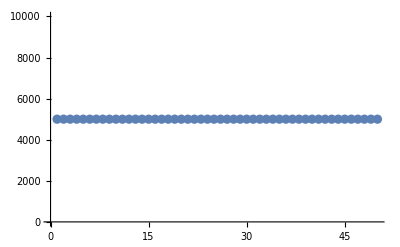

```mathematica
ListPlot[visualRange]
```

```mathematica
Exort[FileNameJoin[{NotebookDirectory[],"daylightVisualRange.csv"}],pupilvsRange];
```

```mathematica
Cz[r_]:=(
```